```mathematica
(* This notebook contains examples for the PET-function;
-MinDat-           return thermodynamic standard state properties of a phase;
-MinList-          list all phases available in the data set;
-G-                calculate the G-function of a phase;
-RTlnf-            calculate properties of pure fluids 
*)
(* This top-cell must be run once before any example can be performed.  *)

(* Define the directory,where the PET-files reside (e.g. C:\Eigene Dateien\Pet) and load PET. *)$PetDirectory="C:\Dokumente und Einstellungen\dachsedgar\Eigene Dateien\Pet\Pet7.0";

SetDirectory[$PetDirectory];
DeclarePackage["DEFDAT`",{"Dataset"}];
Dataset[Dataset-> B88];
```

```mathematica
(* display the usage for the PET-functions -MinDat-  *) 
MinDat::usage
```

MinDat[min] reads thermodynamic data of the phase <min>.
Mineral abbreviations as returned by MinList[] must be used for proper phase identification.

--------------------------------------------------------------------------------------------------
Berman (1988) data set (file THDATB.m):
The data have been transformed from the TWEEQ file "jan92.rgb" and have a similar structure.
Data appear as a list for each phase-component, consisting of the elements:

{{"PHASE_COMPONENT_NAME", abbreviation, "chemistry","mineral-group (optional, may be empty string)"},
{ST    (standard state properties), G,  H,  S,  V,  number (units: [J/mol], [J/mol], [J/(mol.K)], [J/bar])},
{C1     (coefficients for cp-term), ko, k1, k2, k3, number},
{V1 (coefficients for volume-term), v3, v4, v1, v2, number}}

Additional terms that may appear are:
{C2  (additional cp-coefficients), k4, k5, number, number, number}
{C3 (Maier-Kelly cp-coefficients), ko, k5, k2,     number, number}

See G::usage for more details on the form of cp-equation, volume equation, etc.
Special case phases are:
lambda-transitions: ak, crst, hem, kal, lc, mt, ne, qz, try
order/disorder:     ab, dol, geh, kf
(for these phases there appear additional terms labeled T1, T2, T3 and D1, D2;
see TWEEQ documentation for more details on the meaning of these terms).

Example for muscovite: MinDat[mu]
{{"MUSCOVITE", mu, "K(1)AL(3)SI(3)O(12)H(2)","wm"},
{ST, (-5.599784*^6),(-5.97674012*^6), 293.1567, 14.087, 1.},
{C1, 651.48926, (-3873.229), (-1.85232*^7), 2.742469376*^9, 0.},
{V1, 3.35273302, 0., (-0.17169021), 0.00042947, 0.}})

--------------------------------------------------------------------------------------------------
Holland & Powell (1998) data set (file THDATHP*.m):
The data have been transformed from the THERMOCALC_3.* file "th.pd".
Data appear as a list for each phase-component, consisting of the elements:

{{"PHASE_COMPONENT_NAME", abbreviation, "chemistry","mineral-group (optional, may be empty string)"},
{H [J/mol],  S [J/(mol.K)],  V [J/bar]},
{coefficients for cp-term: a, b, c, d},
{parameters for volume-term: ao, a1}}

A fifth term that may appear is for special case phases:
order/disorder- or lambda transition phases:
{T(c0), Smax, Vmax}
aqueous species:
{cpo}
See Holland & Powell (1998) for the meaning of these parameters.
Example for muscovite: MinDat[mu]
{{"MUSCOVITE", mu, "K(1)AL(3)SI(3)O(12)H(2)","wm"},
{(-5.98419*^6), 292., 14.083},
{756.4, -0.01984, -2.17*^6, -6979.2},
{0.0000596, 490000.}}

--------------------------------------------------------------------------------------------------
Gottschalk (1997) data set (file THDATG.m):
The data have been transformed from the file conset-tab.txt (downloaded from http://www.gfz-potsdam.de/pb4/pg1/dataset/).
Data appear as a list for each phase-component, consisting of the elements:

{{"PHASE_COMPONENT_NAME", abbreviation, "chemistry","mineral-group (optional, may be empty string)"},
{H [kJ/mol],  S [J/(mol.K)],  V [1/(MPa.mol)]},
{{coefficients for cp-term: Tmin, Tmax, a, b, c, d, e, f, g},...},
{parameters for volume-term: ao, a1, bo, b1}}

See Gottschalk (1997) for the meaning of these parameters.
{{"MUSCOVITE ", mu, "K(1)Al(3)Si(3)O(12)H(2)", "wm"},
{-5987.024, 287.199, 140.71},
{{298, 1000, 917.67, -0.08111, 0., -10348., 0., 2.8341*^6, 0.},
 {1000, 1800, 651.49, 0., 0., -3873.2, 0., -1.85232*^7, 2.74247*^9}},
{0.000032, 0., 0.000012, 0.}}

Called from: User, -G-, -GB-, -GHP-, -GGot-.
Package name: G.m
PET: Petrological Elementary Tools, (c) Edgar Dachs.

```mathematica
(* Example 1: Use the PET function -MinDat- to display the thermodynamic properties of muscovite
for the Berman, the Holland & Powell and the Gottschalk data set *)
Dataset[Dataset-> B88]; 
MinDat[mu]
Dataset[Dataset->HP32]; 
MinDat[mu]
Dataset[Dataset->G97]; 
MinDat[mu]
```

{{MUSCOVITE,mu,K(1)AL(3)SI(3)O(12)H(2),wm},{ST,-5.59978×10^6,-5.97674×10^6,293.157,14.087,1.},{C1,651.489,-3873.23,-1.85232×10^7,2.74247×10^9,0.},{V1,3.35273,0.,-0.17169,0.00042947,0.}}

{{MUSCOVITE,mu,K(1)Al(3)Si(3)O(12)H(2),wm},{-5.98418×10^6,292.,14.083},{756.4,-0.01984,-2.17×10^6,-6979.2},{0.0000596,490000.}}

{{MUSCOVITE ,mu,K(1)Al(3)Si(3)O(12)H(2),wm},{-5987.02,287.199,140.71},{{298,1000,917.67,-0.08111,0.,-10348.,0.,2.8341×10^6,0.},{1000,1800,651.49,0.,0.,-3873.2,0.,-1.85232×10^7,2.74247×10^9}},{0.000032,0.,0.000012,0.}}

```mathematica
(* Example 2: Use the PET function -MinList- to display all available phases in the B88 data set and their abbreviation *)
Dataset[Dataset-> B88]; 
MinList[]
```

{{AKERMANITE,ak},{ALBITE,ab},{ALBITE_HIGH,abh},{ALBITE_LOW,abl},{ALEUCITE,lc},{ALMANDINE,alm},{ALPHA_CRISTOBALITE,crst},{ANDALUSITE,and},{ANDRADITE,andr},{ANNITE,ann},{ANORTHITE,an},{ANTHOPHYLLITE,anth},{ANTIGORITE,atg},{A-QUARTZ,qz},{BADDELYITE,bdy},{BETA_CRISTOBALITE,crstb},{BLEUCITE,lcb},{B-QUARTZ,qzb},{BRUCITE,br},{CA_AL_PYROXENE,cats},{CALCITE,cal},{CARBON_DIOXIDE,co2},{CHRYSOTILE,chr},{CLINOCHLORE,clin},{CLINOENSTATITE,enc},{CLINOZOISITE,zoc},{COESITE,coe},{CORDIERITE,crd},{CORDIERITE_DRY,crda},{CORUNDUM,cor},{DIASPORE,dsp},{DIOPSIDE,di},{DOLOMITE,dol},{FAYALITE,fa},{FE_CORDIERITE,fcrd},{FE_CORDIERITE_DRY,fcrda},{FE_PARGASITE,fprg},{FERROSILITE,fs},{FE_TREMOLITE,fact},{FE_TSCHERMAKITE,fts},{FORSTERITE,fo},{GEHLENITE,geh},{GEIKELITE,geik},{GLAUCOPHANE,gl},{GROSSULAR,gr},{HEDENBERGITE,hed},{HEMATITE,hem},{HERCYNITE,herc},{HIGH_TRIDYMITE,tryh},{HYDROGEN_GAS,h2},{ILMENITE,ilm},{JADEITE,jd},{KALSILITE,kal},{KAOLINITE,kao},{K-FELDSPAR,kf},{K-FELDSPAR_HIGH,san},{K-FELDSPAR_LOW,mic},{KYANITE,ky},{LAWSONITE,law},{LIME,lime},{LOW_TRIDYMITE,try},{MAGNESITE,mag},{MAGNETITE,mt},{MARGARITE,ma},{MEIONITE,me},{MERWINITE,merw},{MONTICELLITE,mont},{MUSCOVITE,mu},{NEPHELINE,ne},{ORTHOENSTATITE,en},{OXYGEN_GAS,o2},{PARAGONITE,pa},{PARGASITE,prg},{PERICLASE,per},{PHLOGOPITE,phl},{PREHNITE,pre},{PROTOENSTATITE,enp},{PSEUDOWOLLASTONITE,pswo},{PUMPELLYITE,pump},{PYROPE,py},{PYROPHYLLITE,pyp},{RUTILE,ru},{SILLIMANITE,sil},{SPHENE,sph},{SPINEL,spi},{STAUROLITE,fst},{SULFUR_GAS,s2},{TALC,ta},{TREMOLITE,tr},{TSCHERMAKITE,ts},{WATER,h2o},{WOLLASTONITE,wo},{ZIRCON,zrc},{ZOISITE,zo}}

```mathematica
(* display the usage for the PET-functions -G-  *) 
G::usage
```

G[min, P(bar), T(K)] calculates thermodynamic functions of a phase.
<min> is the phase abbreviation as returned by MinList[].
The RTlnf-term for fluids is appended (see Fugacity::usage for more details).

The following data sets are available,                activated with the function -Dataset-:

Berman (1988) J Petrol 29: 445-522                    Dataset[Dataset -> B88]
Holland & Powell (1998) J metam Geol 16:309-343       Dataset[Dataset -> HP31], or
                                                      Dataset[Dataset -> HP32]
Gottschalk (1997) Eur J Mineral 9: 175-223            Dataset[Dataset -> G97]

The Berman (1988) data set has been transformed from the TWEEQ-file "jan92.rgb".
"31" or "32" following "HP" indicates that the thermodynamic data have been
converted from the file "th.pd" of THERMOCALC-versions 3.1 or 3.2 respectively. 
The Gottschalk (1997) data set has been transformed from the file "conset-tab.txt"
(downloaded from http://www.gfz-potsdam.de/pb4/pg1/dataset/)
The following option is available with -G-:

Name           value           meaning

ReturnValue -> G (default)     G = H[1,298] + Int[cp]dT -T (S[1,298] +  Int[cp/T]dT) + Int[V]dP
               H               H(T) = H[1,298] + Int[cp]dT
               S               S(T) = S[1,298] + Int[cp/T]dT
               Vint            Int[V]dP + V(disorder) (Berman data set)
                               Int[V]dP + Int[V(Landau)]dP (Holland & Powell data set)
               V               V(P,T) = V[1,298](1+v1(P-1)+v2(P-1)^2+v3(T-298)+v4(T-298)^2)+V(lambda) (Berman data set)
                               V(P,T) + V(Landau) (Holland & Powell data set)
                               V(P,T) = V[1,298]Exp[a1(T-298)-b1*P] (Gottschalk data set)
               Cp              cp(T) = ko + k1 T^-0.5 + k2 T^-2 + k3 T^-3 + k4 T^-1 + k5 T
                                       + cp(lambda) + cp(disorder) (Berman data set)
                               cp(T) = a + b T + c T^-2 + d T^(-1/2) + cp(Landau) (Holland & Powell data set)
                               cp(T) = a + b T + c T^2 + d T^(-0.5) + e/T + f/T^2 + g/T^3 (Gottschalk data set)

See Berman (1988), Holland & Powell (1998) and Gottschalk (1997) for more details
(lambda transitional terms, order/disorder terms, etc.)
Example 1 (Berman data set): G[mu, 5000, 773]
ReturnValue: -6.2343308024*10^6
Example 2 (Berman data set): G[mu, 5000, 773, ReturnValue->Cp]
ReturnValue: 487.117
Called from: -Dgr-, User.
Calls: -MinDat-, -GOrd-, -Gl-, -RTlnf- (Berman data set),
       -GLandau-, -GAqueousSpecies-, -RTlnf- (Holland & Powell data set),
       -GGot- ((Gottschalk data set)).
Package name: G.m
PET: Petrological Elementary Tools, (c) Edgar Dachs.

```mathematica
(* Example 3: Use the PET function -G- to calculate the Gibbs-function for muscovite at P = 5000 bar, T = 773 K *)
(* compare the three data sets *)
Dataset[Dataset-> B88]; 
G[mu,5000,773]
Dataset[Dataset->HP32]; 
G[mu,5000,773]
Dataset[Dataset->G97]; 
G[mu,5000,773]
```

-6.23433×10^6

-6.24108×10^6

-6.2404×10^6

```mathematica
(* Example 4: Use the PET function -G- to calculate the heat capacity for muscovite at P = 5000 bar, T = 773 K *)
G[mu,5000,773, ReturnValue->Cp]
```

487.523

```mathematica
(* Example 5: Use the PET-function -G- to plot the G-surface of sillimanite for pressures between 1 and 10000 bar,and temperatures between 500 and 1000 K; Use the Mathematica built-in function-Plot3D-to make a threedimensional plot. *)
plot=Plot3D[G[sil,p,t],{p,1,10000},{t,500,1000},AxesLabel->{"P(bar)","T(K)"," "}]
```

-Graphics3D-

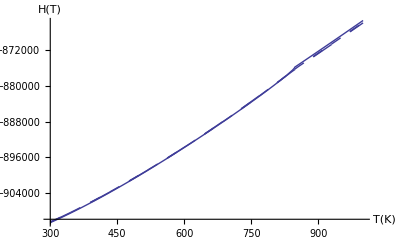

```mathematica
(*  Example 6: Use the PET function -G- to calculate the H(T)-function of quartz
for temperatures between 300 and 1000 K (1 bar); compare the data sets.
Use the Mathematica built-in function -Plot- to plot the results. *)

Dataset[Dataset-> B88];
plot1=Plot[G[qz,1,t,ReturnValue->H],{t,300,1000},AxesLabel->{"T(K)","H(T)"},PlotStyle->{Dashing[{0.02}]}];
Dataset[Dataset-> HP32]; 
plot2=Plot[G[qz,1,t,ReturnValue->H],{t,300,1000},AxesLabel->{"T(K)","H(T)"}];
Dataset[Dataset-> G97]; 
plot3=Plot[G[qz,1,t,ReturnValue->H],{t,300,1000},AxesLabel->{"T(K)","H(T)"},PlotStyle->{Dashing[{0.04}]}];
Show[plot1,plot2,plot3]
```

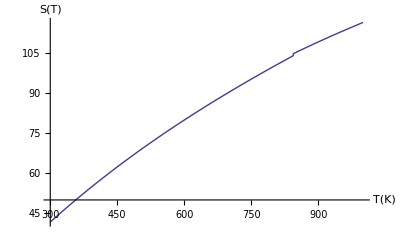

```mathematica
(* Example 7: Use the PET function -G- to calculate the S(T)-function of quartz
for temperatures between 300 and 1000 K (1 bar);
Use the Mathematica built-in function -Plot- to plot the results. *)

plot=Plot[G[qz,1,t,ReturnValue->S],{t,300,1000},AxesLabel->{"T(K)","S(T)"}]
```

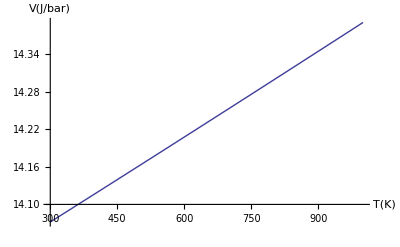

```mathematica
(* Example 8: Use the PET function -G- to calculate the molar volume of muscovite for temperatures between 300 and 1000 K (1 bar);
Use the Mathematica built-in function -Plot- to plot the results. *)

plot=Plot[G[mu,1,t,ReturnValue->V],{t,300,1000},AxesLabel->{"T(K)","V(J/bar)"}]
```

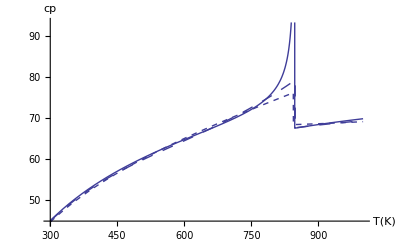

```mathematica
(* Example 9: Use the PET function -G- to calculate cp for quartz for temperatures between 300 and 1000 K. 
Compare the data sets.
Use the Mathematica built-in function -Plot- to plot the results. *)

Dataset[Dataset-> B88];
plot1=Plot[G[qz,1,t,ReturnValue->Cp],{t,300,1000},AxesLabel->{"T(K)","cp"},PlotStyle->{Dashing[{0.02}]}];
Dataset[Dataset-> HP32]; 
plot2=Plot[G[qz,1,t,ReturnValue->Cp],{t,300,1000},AxesLabel->{"T(K)","cp"}];
Dataset[Dataset-> G97]; 
plot3=Plot[G[qz,1,t,ReturnValue->Cp],{t,300,1000},AxesLabel->{"T(K)","cp"},PlotStyle->{Dashing[{0.01}]}];

Show[plot1,plot2,plot3,PlotRange->All]
```

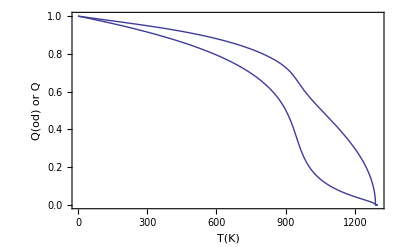

```mathematica
(* Example 10: Use the PET-function -GOrdAb- to plot the order parameters Q and Q(od) for albite as function of temperature according to Salje et al (1985): Phys. Chem. Miner. 12; 99 to 107;
Use the Mathematica built-in functions-Plot-and-Show-to display the graph. *)

plot1=Plot[GOrdAb[t][[4]],{t,0,1300}];
plot2=Plot[GOrdAb[t][[5]],{t,0,1300}];
Show[plot1,plot2,Frame->True,PlotRange->{{0,1300},{0,1}},FrameLabel->{"T(K)","Q(od) or Q"}]
```

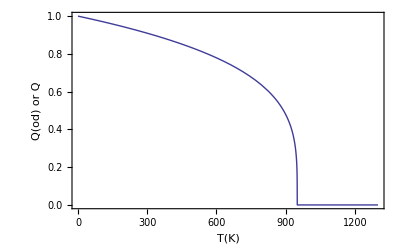

```mathematica
(* Example 10: Note: Use the PET-function -GLandau- to plot the order parameters Q for albite as function of temperature;
Use the Mathematica built-in functions-Plot-and-Show-to display the graph. *)

Dataset[Dataset-> HP32]; 
plot1=Plot[GLandau[ab,1,t,Flatten[Take[MinDat[ab],{4,5}]]][[7]],{t,0,1300}];
Show[plot1,Frame->True,PlotRange->{{0,1300},{0,1}},FrameLabel->{"T(K)","Q(od) or Q"}]
```

```mathematica
(* Example 11: Use the PET function -RTlnf- to calculate RTln(fugacity) of H2O at P and T *)
RTlnf[h2o,5000,800]
```

51551.3

```mathematica
(* Example 12: Use the PET function -RTlnf- to calculate the fugacity of pure H2O at P and T. Compare available models *)
RTlnf[h2o,5000,800,RTlnfReturnValue->Fugacity,RTlnfModel->HaarEtAl84]
RTlnf[h2o,5000,800,RTlnfReturnValue->Fugacity,RTlnfModel->KerrickJacobs81]
RTlnf[h2o,5000,800,RTlnfReturnValue->Fugacity,RTlnfModel->HollandPowell91]
RTlnf[h2o,5000,800,RTlnfReturnValue->Fugacity,RTlnfModel->Holloway77]
```

2322.49

2319.93

2333.29

2334.15

```mathematica
(* Example 13: Use the PET function -RTlnf- to calculate the molar volume of pure H2O at P and T. Compare available models *)
RTlnf[h2o,5000,800,RTlnfReturnValue->Volume,RTlnfModel->HaarEtAl84]
RTlnf[h2o,5000,800,RTlnfReturnValue->Volume,RTlnfModel->KerrickJacobs81]
RTlnf[h2o,5000,800,RTlnfReturnValue->Volume,RTlnfModel->HollandPowell91]
RTlnf[h2o,5000,800,RTlnfReturnValue->Volume,RTlnfModel->Holloway77]
```

21.4047

21.1871

21.3166

21.2493